## Description

Interception of rays by sphere and tube

## Styles

```mathematica
plotStyle={
PlotRangePadding->0,
PlotStyle->Directive[RGBColor["#225F8E"],Thickness[0.005]],
GridLinesStyle->Directive[GrayLevel[0.7],Dashing[0.008]],

Axes->None,
Frame->True,
Filling->Axis,
FrameStyle->Directive[Black,FontFamily->"Arial",FontSize->14],

ImagePadding->{{1.,0.25},{0.75,0.25}}*72,
AspectRatio->0.5
};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## SphericalReceiver

```mathematica
(* import data *)
data=Import["C:\\Neo\\Programming\\SphericalReceiver.csv"];
```

```mathematica
(* normalize data *)
data=data[[All,{2,3}]];
PrependTo[data,{0.,0.}];
energyMax=data[[-1,2]];
data[[All,2]]/=energyMax;
rMax=12;
```

```mathematica
(* interpolate data *)
funcInterception=Interpolation[data];
```

```mathematica
(* find radius for a given interception *)
findRadius[interception_Real]:=Module[{radius},
radius/.FindRoot[funcInterception[radius]==interception,{radius,0,rMax}]
]
```

```mathematica
(* gridlines for interception *)
levels={0.90,0.95};
```

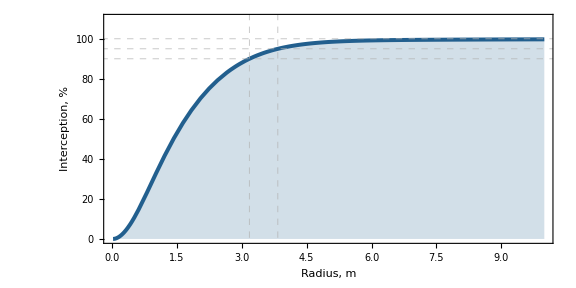

```mathematica
figure=Plot[
100*funcInterception[r],
{r,0,10.},
PlotRange->{{0,10},100*{0,1.10}},
GridLines->{findRadius/@levels,100*Join[levels,{1.}]},
ImageSize->{8,4}*72,
FrameLabel->{"Radius, m","Interception, %"},
Evaluate[plotStyle]
]
```

```mathematica
(*Export["SphericalReceiver.png",figure];*)
```

## TubularReceiver

```mathematica
(* import data *)
data=Import["C:\\Neo\\Programming\\TubularReceiver.csv"];
```

```mathematica
(* normalize data *)
data=data[[All,{2,3}]];
PrependTo[data,{0.,0.}];
energyMax=data[[-1,2]];
data[[All,2]]/=energyMax;
rMax=0.05;
```

```mathematica
(* interpolate data *)
funcInterception=Interpolation[data,InterpolationOrder->3];
```

```mathematica
(* find radius for a given interception *)
findRadius[interception_Real]:=Module[{radius},
radius/.FindRoot[funcInterception[radius]==interception,{radius,0,rMax}]
]
```

```mathematica
(* gridlines for interception *)
levels={0.90,0.95};
```

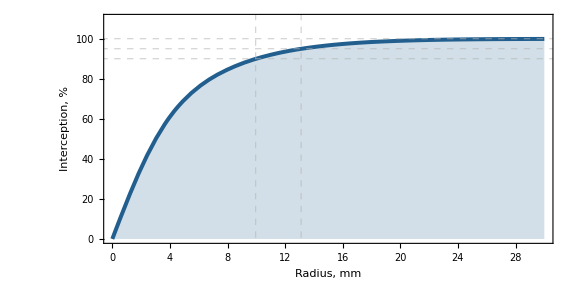

```mathematica
figure=Plot[
100*funcInterception[0.001*r],
{r,0,30},
PlotRange->{Full,100*{0.,1.10}},
GridLines->{1000.*findRadius/@levels,100*Join[levels,{1.}]},
ImageSize->{8,4}*72,
FrameLabel->{"Radius, mm","Interception, %"},
Evaluate[plotStyle]
]
```

```mathematica
(*Export["TubularReceiver.png",figure];*)
```